# ArmandoCruz/ZeroKnowledgeProofs

Implementation of Zero Knowledge proof interactive and non-interactive protocols

## Paclet Manifest

"Documentation"

"ChangeBacklog.md"DocumentationChangeBacklog.md

"ChangeLog.md"DocumentationChangeLog.md

"English"

"Guides"

"ZeroKnowledgeProofs.nb"DocumentationEnglishGuidesZeroKnowledgeProofs.nb

"ReferencePages"

"Symbols"

"AnswerZeroKnowledgeQuery.nb"DocumentationEnglishReferencePagesSymbolsAnswerZeroKnowledgeQuery.nb

"CompileArithmeticCircuit.nb"DocumentationEnglishReferencePagesSymbolsCompileArithmeticCircuit.nb

"CompileQuadraticArithmeticProgram.nb"DocumentationEnglishReferencePagesSymbolsCompileQuadraticArithmeticProgram.nb

"EvaluateArithmeticCircuitSolution.nb"DocumentationEnglishReferencePagesSymbolsEvaluateArithmeticCircuitSolution.nb

"GenerateZeroKnowledgePrivateSolution.nb"DocumentationEnglishReferencePagesSymbolsGenerateZeroKnowledgePrivateSolution.nb

"GenerateZeroKnowledgeProof.nb"DocumentationEnglishReferencePagesSymbolsGenerateZeroKnowledgeProof.nb

"GenerateZeroKnowledgeQuery.nb"DocumentationEnglishReferencePagesSymbolsGenerateZeroKnowledgeQuery.nb

"GenerateZeroKnowledgeWitness.nb"DocumentationEnglishReferencePagesSymbolsGenerateZeroKnowledgeWitness.nb

"VerifyZeroKnowledgeProof.nb"DocumentationEnglishReferencePagesSymbolsVerifyZeroKnowledgeProof.nb

"ZeroKnowledgeCipherProblem.nb"DocumentationEnglishReferencePagesSymbolsZeroKnowledgeCipherProblem.nb

"ZeroKnowledgeCipherSolution.nb"DocumentationEnglishReferencePagesSymbolsZeroKnowledgeCipherSolution.nb

"ZeroKnowledgePrivateSolution.nb"DocumentationEnglishReferencePagesSymbolsZeroKnowledgePrivateSolution.nb

"ZeroKnowledgePublicProblem.nb"DocumentationEnglishReferencePagesSymbolsZeroKnowledgePublicProblem.nb

"ZeroKnowledgeQuery.nb"DocumentationEnglishReferencePagesSymbolsZeroKnowledgeQuery.nb

"ZeroKnowledgeResponse.nb"DocumentationEnglishReferencePagesSymbolsZeroKnowledgeResponse.nb

"Tutorials"

"ZeroKnowledgeAuthentication.nb"DocumentationEnglishTutorialsZeroKnowledgeAuthentication.nb

"zkSNARKCompilation.nb"DocumentationEnglishTutorialszkSNARKCompilation.nb

"Kernel"

"InteractiveProofs"

"InteractiveProofs.wl"KernelInteractiveProofsInteractiveProofs.wl

"Protocols"

"Isomorphism.wl"KernelInteractiveProofsProtocolsIsomorphism.wl

"Symbols.wl"KernelSymbols.wl

"ZeroKnowledgeProofs.wl"KernelZeroKnowledgeProofs.wl

"zkSNARK"

"zkSNARK.wl"KernelzkSNARKzkSNARK.wl

"LICENCE"LICENCE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

### Basic Description

This project implements interactive and non interactive zero knowledge proof protocols based on current Wolfram's cryptography framework. Zero knowledge proofs are communication protocols by which one person called the Prover can convince another person called Verifier that it posses a solution to a given public problem without revealing the content of the solution. 

This project implements two main applications of zero knowledge proofs; online zero knowledge authentication that provides protection against 'man in the middle' impersonation attacks; and the most impressive, a Verifier can be convinced that a computation was executed correctly without executing it and without knowing what was executed.

### Details

Additional information about the paclet.

### Primary Context

MyPublisherID`MyPaclet`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[];
```

```mathematica
Needs[];
```

### Interactive proofs

Generate a PrivateSolution and a PublicProblem with an interactive protocol:

```mathematica
zkProof=GenerateZeroKnowledgeProof["Isomorphism"]
```

<|ZeroKnowledgePublicProblem→ZeroKnowledgePublicProblem[…],ZeroKnowledgePrivateSolution→ZeroKnowledgePrivateSolution[…]|>

The Isomorphism protocol is based in finding an isomorphism between to public graphs. The private solution being the isomorphism between them.

A pair of isomorphic graphs.

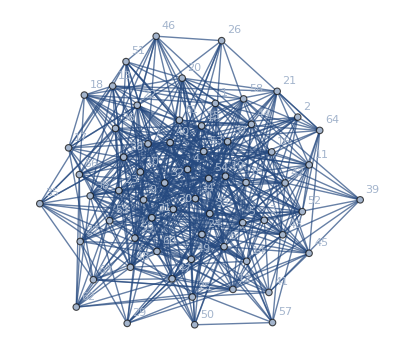
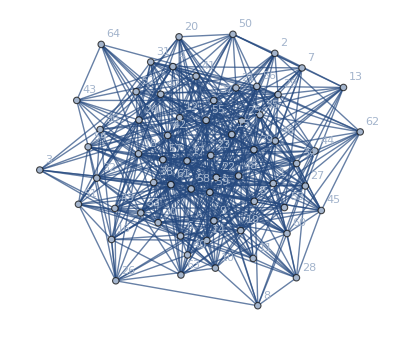

```mathematica
zkProof["ZeroKnowledgePublicProblem"]["PublicProblemShape"]
zkProof["ZeroKnowledgePublicProblem"]["PublicProblem"]
```

Generate an interactive witness that will take the PrivateSolution and generate 3 homomorphic CipherProblems:

```mathematica
witness=GenerateZeroKnowledgeWitness[zkProof["ZeroKnowledgePrivateSolution"],"WitnessSize"->3]
```

<|ZeroKnowledgeCipherProblem→ZeroKnowledgeCipherProblem[…],ZeroKnowledgeCipherSolution→ZeroKnowledgeCipherSolution[…]|>

The homomorphic problems generated by the GXOR algorithm are new pairs of isomorphic graphs  generated by adding noise to the original public pair.

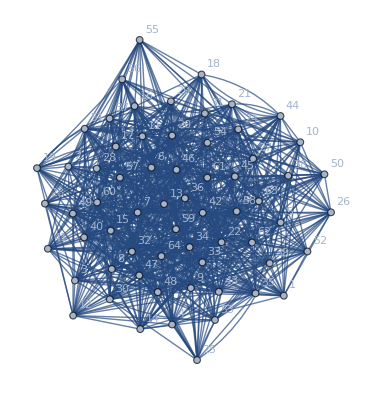
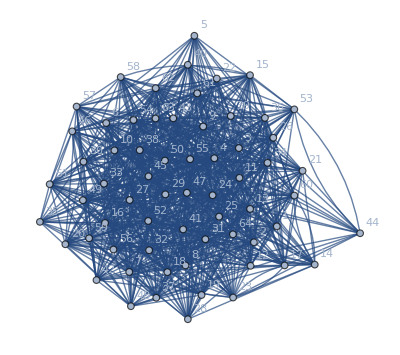

```mathematica
witness["ZeroKnowledgeCipherSolution"]["PublicCipherProblem"][[1]]
```

Cipher solutions consists of an isomorphism  between the cipher problem graphs  and the random noise seed key.

```mathematica
witness["ZeroKnowledgeCipherSolution"]["PrivateCipherSolution"][[1]]
```

<|CipherSolution→{1→63,2→24,3→5,4→21,5→28,6→26,7→25,8→41,9→47,10→58,11→12,12→53,13→8,14→18,15→4,16→39,17→19,18→38,19→36,20→62,21→42,22→14,23→57,24→34,25→15,26→45,27→17,28→50,29→30,30→31,31→33,32→64,33→27,34→55,35→20,36→35,37→9,38→13,39→40,40→52,41→16,42→37,43→11,44→48,45→23,46→43,47→1,48→51,49→44,50→60,51→2,52→56,53→54,54→22,55→46,56→32,57→49,58→29,59→59,60→61,61→3,62→7,63→10,64→6},CipherKey→311504476528031730435665715050243319443181290374|>

The verifier then generate a query to the prover's public witness asking  either for the solution to the cipher problem or the random noise seed key.

```mathematica
query=GenerateZeroKnowledgeQuery[witness["ZeroKnowledgeCipherProblem"]]
query["Query"]
```

ZeroKnowledgeQuery[…]

{1,1,1}

The prover answers the query using the witness knowledge of the CipherSolutions and CipherKeys.

```mathematica
response=AnswerZeroKnowledgeQuery[witness["ZeroKnowledgeCipherSolution"],query]
```

ZeroKnowledgeResponse[…]

```mathematica
response["Response"]
```

{311504476528031730435665715050243319443181290374,403191789230156973464625278098075373999683894575,33377874629286114575285819154636076900465708498}

Verify the proof:

```mathematica
VerifyZeroKnowledgeProof[
zkProof["ZeroKnowledgePublicProblem"],
witness["ZeroKnowledgeCipherProblem"],
"query"->query,
"response"->response
]
```

{True,True,True}

```mathematica
And@@%
```

True

### zk-SNARK

Compile arithmetic problems into corresponding arithmetic circuits:

```mathematica
circuit=CompileArithmeticCircuit[
{(c1-c2)(c1-c3)(c1-c4)(c1-c5)(c2-c5)(c2-c3)(c3-c4)(c4-c5),
Plus@@Table[ci="c"<>ToString[i];(1-ci)(2-ci)(3-ci),{i,5}]},
<|"c1"->1,"c2"->2,"c3"->3,"c4"->2,"c5"->3|>
];
circuit["circuit"][[1]]
```

-Graphics-

```mathematica
EvaluateArithmeticCircuitSolution[circuit][[1]]
```

-Graphics-

Compile the Arithmetic circuit into a Quadratic Arithmetic Program (QAP):

```mathematica
qap=CompileQuadraticArithmeticProgram[circuit];
N@qap["v"]["c2"]
```

-9.78626×10^13+4.61708×10^14 x-1.00964×10^15 x^2+1.3769×10^15 x^3-1.32607×10^15 x^4+9.66753×10^14 x^5-5.5785×10^14 x^6+2.62852×10^14 x^7-1.03491×10^14 x^8+3.46565×10^13 x^9-1.00108×10^13 x^10+2.52297×10^12 x^11-5.60029×10^11 x^12+1.10358×10^11 x^13-1.94366×10^10 x^14+3.0773×10^9 x^15-4.40172×10^8 x^16+5.71316×10^7 x^17-6.75447×10^6 x^18+729844. x^19-72291.1 x^20+6581.14 x^21-551.943 x^22+42.7333 x^23-3.05997 x^24+0.202982 x^25-0.0124914 x^26+0.000714047 x^27-0.0000379566 x^28+1.87804×10^-6 x^29-8.65639×10^-8 x^30+3.71941×10^-9 x^31-1.49059×10^-10 x^32+5.57413×10^-12 x^33-1.94563×10^-13 x^34+6.34004×10^-15 x^35-1.92886×10^-16 x^36+5.47854×10^-18 x^37-1.45248×10^-19 x^38+3.59338×10^-21 x^39-8.29202×10^-23 x^40+1.78376×10^-24 x^41-3.57453×10^-26 x^42+6.66706×10^-28 x^43-1.15619×10^-29 x^44+1.86198×10^-31 x^45-2.78067×10^-33 x^46+3.84446×10^-35 x^47-4.91133×10^-37 x^48+5.78472×10^-39 x^49-6.26581×10^-41 x^50+6.22308×10^-43 x^51-5.64788×10^-45 x^52+4.66543×10^-47 x^53-3.49144×10^-49 x^54+2.3542×10^-51 x^55-1.42091×10^-53 x^56+7.61645×10^-56 x^57-3.59098×10^-58 x^58+1.47136×10^-60 x^59-5.1594×10^-63 x^60+1.51724×10^-65 x^61-3.63919×10^-68 x^62+6.83704×10^-71 x^63-9.43543×10^-74 x^64+8.50496×10^-77 x^65-3.75661×10^-80 x^66

```mathematica
Table[qap["w"]["c2"]/.x->i,{i,Length[circuit["gates"]]}]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

The generated QAP satisfies the characteristic property: V(x)W(x)-K(x)=T(x)=F(x)H(x) for some polynomial H:

```mathematica
R=PolynomialRemainder[qap["F"],qap["T"],x]
```

0

```mathematica
{qap["F"],qap["T"],qap["H"]}/.x->{34,69}//N
```

{{0.,-1.17348×10^43},{0.,2.48004×10^96},{-1.23396×10^-74,-4.73171×10^-54}}

### Scope

## Source & Additional Information

### Creator

Armando Benjamín Cruz Hinojosa

### Source Control Repository

https://github.com/Aleph-GORY/ZeroKnowledgeProofs

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Zero knowledge proof

zkSNARK

Authentication

NP-complete

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.